# Week 3:

## Sunday 24/3

Plotting Phase-Space

```mathematica
V=m g l(1-Cos[ϕ]);
T=(m l^2)/2(D[ϕ[t],t])^2;
H=T+V;
m=1;g=1;l=1;
f1=Table[H==k/.{ϕ[t]-> ϕ,ϕ'[t]-> p},{k,0,20,0.2}];
```

```mathematica
ContourPlot[Evaluate[f1],{ϕ,-π,π},{p,-π,π}]
```

Finding Time-Period - Series

```mathematica
k=Sin[ϕ1/2];
z=Sin[ϕ/2]/k/.ϕ1-> 0.2π;
```

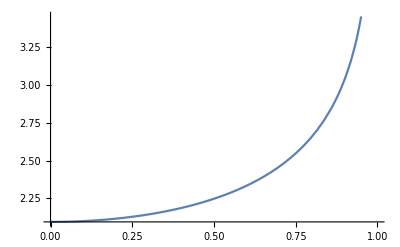

```mathematica
T1=4/ω0 Integrate[1/(√((1-z^2)(1-k^2 z^2))),{z,0,1}, Assumptions-> {k>0 && k<1}]/. ω0-> 3;
Plot[T1,{k,0,1}]
```

```mathematica
S1=Series[T1,{k,0,10}];
res1=Normal[S1];
```

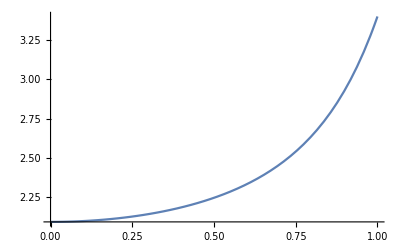

```mathematica
Plot[res1,{k,0,1}]
```

```mathematica
f1=Normal[Series[1/(√((1-z^2)(1-k^2 z^2))),{k,0,10}]];
T2=Expand[4/ω0 Integrate[f1,{z,0,1}, Assumptions-> {k>0 && k<1}]];
```

Expand = Expands T2 as a function different powers of k.

A bit about Mathematica

Mathematica “remembers” functions in tree forms - TreeForm[a]
The “head” of the tree is f - Head[a].
The function Part and [[]] are the same : Part[a,2,1]= a[[2,1]]
Which means - take the second part of a and choose section one of it.
MORE INFO IN THE LECTURES NOTES.

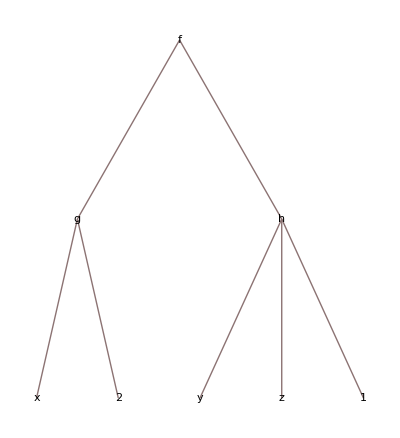

```mathematica
a=f[g[x,2],h[y,z,1]];
TreeForm[a]
Head[a]
```

## Tuesday 26/3

Iterative functions:

One can build an iterative function as “factorial” like  so:

```mathematica
fac[0]=1;
fac[n_]:=n fac[n-1];
fac[3]
```

Solving analytically the mathematical pendulum:

```mathematica
eq=DSolve[ϕ''[t]==-ω^2 Sin[ϕ[t]],ϕ[t],t];
eq1=eq[[1]]/. {C[1]-> 1 , C[2]-> 1, ω-> 1};
```

```mathematica
s1=Normal[N[Series[-2 JacobiAmplitude[1/2 √3 √((1+t)^2),4/3],{t,0,4}]]]//Chop
```

-1.48948-1.07817 t+0.498348 t^2+0.0145964 t^3-0.051649 t^4

Instead of  //Chop one can use the function - ComplexExpand[Re[s1]]
N[]  transform Analytic expressions like sin or the KacobiAmplitude into numbers - like the one I got in the end.

Solving numerically the mathematical pendulum:

Now I write ϕ as x, I will take the same initial conditions as for the analytical solution - x[0]=-1.48948 and x’[0]=-1.07817 and ω=1.

```mathematica
x=x0+Sum[a[i] t^i,{i,4}]+O[t]^5;
D[x,{t,2}]+ω^2 Sin[x]==0;
LogicalExpand[%];
sol=Solve[%]/.ω-> 1;
res1=x/.sol[[1]];
a[1]=-1.07817; x0=-1.48948;
N[res1]//Chop
```

-1.48948-1.07817 t+0.498348 t^2+0.014596 t^3-0.0516487 t^4+O[t]^5

Which is The same as we got when we solved the equation analytically.

# Week 4:

## Sunday 31/3

## Another way to solve the mathematical pendulum:

With a series without LogicalExpand and without O[t]^5:

```mathematica
y=x00+Sum[a[i]t^i,{i,4}];
eq=D[y,{t,2}]==-(ω^2)[y-y^3/6];
a[1]=1; x00=1;
eq1=eq/.t->0;
a2=Solve[eq1,a[2]];
eq2=D[eq,t]/.t->0;
a3=Solve[eq2,a[3]];
eq3=D[eq,{t,2}]/.t->0;
a4=Solve[eq3,a[4]];
```

With a series, with LogicalExpand and with expanding X by ϵ coefficients:

```mathematica
X= Sum[ ϵ^i Subscript[x, i][t],{i,4}] +O[ϵ]^5;
Eq=D[X,{t,2}]==-ω0^2 X-α2 X^2-α3 X^3;
Res=LogicalExpand[%];
Res1=Res/.And-> List;
Res1=MatrixForm[Res1]
DSolve[Res1[[1,1]],Subscript[x, 1][t],t]
```

(ω0^2 x_1[t]+x_1''[t]==0
α2 x_1[t]^2+ω0^2 x_2[t]+x_2''[t]==0
α3 x_1[t]^3+2 α2 x_1[t] x_2[t]+ω0^2 x_3[t]+x_3''[t]==0
3 α3 x_1[t]^2 x_2[t]+α2 (x_2[t]^2+2 x_1[t] x_3[t])+ω0^2 x_4[t]+x_4''[t]==0)

{{x_1[t]→C[1] Cos[t ω0]+C[2] Sin[t ω0]}}

With the same as above but without LogicalExpand - using derivatives:

Exists in Alex’s notes - Didn’t have time to finish writing it in class.

## Tuesday 2/4

Initial Conditions:

```mathematica
IC=(X/.t->0 )==ϵ x0 && (D[X,t]/.t->0 )==ϵ v0;
resa=LogicalExpand[IC];
resb=resa/. And-> List;
resbM=MatrixForm[resb];
Solve[resb];
resc1=DSolve[{Res1[[1,1]],Subscript[x, 1][0]==x0,Subscript[x, 1]'[0]== v0},Subscript[x, 1][t],t];
Res1[[1,2]];
resc2=DSolve[{α2 ((x0 ω Cos[t ω]+v0 Sin[t ω])/ω)^2+ω^2 Subscript[x, 2][t]+Subscript[x, 2]''[t]==0,Subscript[x, 2][0]==x0,Subscript[x, 2]'[0]== 0},Subscript[x, 2][t],t]
Simplify[resc2]
```

{{x_2[t]→1/(12 ω^4)(8 v0^2 α2 Cos[t ω]+4 x0^2 α2 ω^2 Cos[t ω]+12 x0 ω^4 Cos[t ω]-9 v0^2 α2 Cos[t ω]^2-3 x0^2 α2 ω^2 Cos[t ω]^2+v0^2 α2 Cos[t ω] Cos[3 t ω]-x0^2 α2 ω^2 Cos[t ω] Cos[3 t ω]-8 v0 x0 α2 ω Sin[t ω]+6 v0 x0 α2 ω Cos[t ω] Sin[t ω]+2 v0 x0 α2 ω Cos[3 t ω] Sin[t ω]-3 v0^2 α2 Sin[t ω]^2-9 x0^2 α2 ω^2 Sin[t ω]^2+8 v0 x0 α2 ω Cos[t ω] Sin[t ω]^3+v0^2 α2 Sin[t ω] Sin[3 t ω]-x0^2 α2 ω^2 Sin[t ω] Sin[3 t ω])}}

{{x_2[t]→1/(6 ω^4)(2 (2 v0^2 α2+x0 ω^2 (x0 α2+3 ω^2)) Cos[t ω]-α2 (3 v0^2+3 x0^2 ω^2+(v0^2-x0^2 ω^2) Cos[2 t ω]+4 v0 x0 ω Sin[t ω]-2 v0 x0 ω Sin[2 t ω]))}}

x_1[t] ϵ+x_2[t] ϵ^2+x_3[t] ϵ^3+x_4[t] ϵ^4+O[ϵ]^5==x0 ϵ&&0==v0 ϵ

# Week 5:

## Sunday 7/4

Amplitude as a function of frequency

```mathematica
ω= Sum[ϵ^i  Subscript[w, i],{i,0,3}]+O[ϵ]^4;
Y= Sum[ ϵ^i Subscript[y, i][t],{i,3}] +O[ϵ]^4;
eq=ω^2  D[Y,{t,2}] ==-Subscript[w, 0]^2 Y-Subscript[α, 2] Y^2-Subscript[α, 3] Y^3;
res=LogicalExpand[eq]/. And-> List//MatrixForm
resy1= DSolve[{res[[1,1]],Subscript[y, 1][0]==1,Subscript[y, 1]'[0]==1},Subscript[y, 1][t],t][[1]]

exp1=FullSimplify[res[[1,2]]/.resy1[[1]]/.Subscript[y, 1]''[t]-> D[Subscript[y, 1][t]/.resy1[[1]],{t,2}],Assumptions->{Subscript[w, 0]>0}];
```

(w_0^2 y_1[t]+w_0^2 y_1''[t]==0
α_2 y_1[t]^2+w_0^2 y_2[t]+2 w_0 w_1 y_1''[t]+w_0^2 y_2''[t]==0
α_3 y_1[t]^3+2 α_2 y_1[t] y_2[t]+w_0^2 y_3[t]+(w_1^2+2 w_0 w_2) y_1''[t]+2 w_0 w_1 y_2''[t]+w_0^2 y_3''[t]==0)

{y_1[t]→Cos[t]+Sin[t]}

In order to prevent divergence  we take   w_1to 0:

```mathematica
exp2=exp1/.Subscript[w, 1]-> 0;
resy2=FullSimplify[DSolve[{exp2,Subscript[y, 2][0]==0,Subscript[y, 2]'[0]==0},Subscript[y, 2][t],t]]//TrigReduce
exp3=FullSimplify[res[[1,3]]/.resy1[[1]]/.Subscript[y, 1]''[t]-> D[Subscript[y, 1][t]/.resy1[[1]],{t,2}]/. resy2[[1]]/.Subscript[w, 1]-> 0];
```

{{y_2[t]→(-3 α_2+3 Cos[t] α_2-2 Sin[t] α_2+Sin[2 t] α_2)/(3 w_0^2)}}

(Cos[t]+Sin[t])^3 α_3+w_0^2 (y_3[t]+y_3''[t])==2 (Cos[t]+Sin[t]) w_0 w_2+(4 Sin[t/2]^2 (1+3 Cos[t]-Cos[2 t]+3 Sin[t]+Sin[2 t]) α_2^2)/(3 w_0^2)

# Week 6 - Sunday 14/4:

Complex Integrals

Every function can be written as a Lorentz serie - f(z)=∑_(n=-∞)^∞ (a_n(z-a))^n,  ⟶ ∫f(z)ⅆz = ∑_(n=-∞)^∞ a_n∫_0^(2π) iⅇ^it/ⅇ^itn ⅆt =2π i a_-1

```mathematica
z[t_]=Exp[I t]
f[z_,n_]:=z^n
sol=Table[Integrate[f[z[t],n] z'[t],{t,0,2π}],{n,-10,10}]
```

ⅇ^(ⅈ t)

{0,0,0,0,0,0,0,0,0,2 ⅈ π,0,0,0,0,0,0,0,0,0,0,0}

### Lorentzian:

```mathematica
f[z_]=1/(1+z^2);

u[{x_,y_}]=FullSimplify[ComplexExpand[Re[f[x+I y]]]];
v[{x_,y_}]=FullSimplify[ComplexExpand[Im[f[x+I y]]]];
ϕ[{x_,y_}]={u[{x,y}],v[{x,y}]};
ϕ̄[{x_,y_}]={u[{x,y}],-v[{x,y}]};
SuperStar[ϕ][{x_,y_}]={v[{x,y}],u[{x,y}]};
Subscript[x, z0_,R_][t_]:=Re[z0]+R Cos[t]
Subscript[y, z0_,R_][t_]:=Im[z0]+R Sin[t]
Subscript[Z, z0_,R_][t_]:=Subscript[x, z0,R][t]+I Subscript[y, z0,R][t]
Subscript[r, z0_,R_][t_]:={Subscript[x, z0,R][t], Subscript[y, z0,R][t]}
```

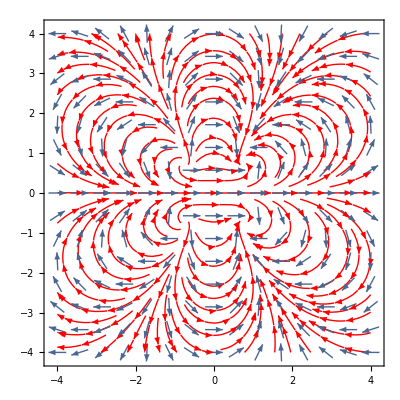

```mathematica
g1=StreamPlot[ϕ̄[{x,y}],{x,-4,4},{y,-4,4},StreamStyle->  Red];
g2=VectorPlot[ϕ̄[{x,y}],{x,-4,4},{y,-4,4}, VectorScale->{0.04,0.7,None}];
Show[g1,g2]
```

```mathematica
f[z_]=1/(1+z^4);
u[{x_,y_}]=FullSimplify[ComplexExpand[Re[f[x+I y]]]];
v[{x_,y_}]=FullSimplify[ComplexExpand[Im[f[x+I y]]]];
ϕ[{x_,y_}]={u[{x,y}],v[{x,y}]};
ϕ̄[{x_,y_}]={u[{x,y}],-v[{x,y}]};
SuperStar[ϕ][{x_,y_}]={v[{x,y}],u[{x,y}]};
sol1=Solve[z^4==-1,z];
res1=Residue[f[z],{z,-(-1)^(1/4)}];
res2=Residue[f[z],{z,(-1)^(1/4)}];
res3=Residue[f[z],{z,-(-1)^(3/4)}];
res4=Residue[f[z],{z,(-1)^(3/4)}];
integral= (res4+res3)2π I
```

0